```mathematica
(y-x y-x^2)//FullSimplify
(x-x y-y^2)//FullSimplify
```

y-x (x+y)

x-x y-y^2

```mathematica
∫_0^(1-x) (y-x y-x^2)/(x+y)^2 ⅆy
∫_0^(1-x) (x-x y-y^2)/(x+y)^2 ⅆy
```

ConditionalExpression[(-1+x) (1+Log[x]), ]

ConditionalExpression[-x Log[x], ]

```mathematica
(-1+x) (1+Log[x])//Expand
```

-1+x-Log[x]+x Log[x]

```mathematica
∫_0^1 (-1+x) (1+Log[x])ⅆx
∫_0^1 -x Log[x]ⅆx
```

1/4

1/4

```mathematica
∫_0^1 (3 x^2+2x y +y^2)ⅆy
```

1/3+x+3 x^2

```mathematica
∫_0^1 %ⅆx
```

11/6

```mathematica
N[11/6]
```

1.83333

```mathematica
N[11/6, 13]
```

1.833333333333

```mathematica
N[11/6,17]
```

1.8333333333333333

```mathematica
MM={{1,2,3,4},{5,6,7,8}}//MatrixForm
HH={1,2}//MatrixForm
```

(1 | 2 | 3 | 4
5 | 6 | 7 | 8)

(1
2)

```mathematica
Transpose[HH]//MatrixForm
```

Transpose[(1
2
3
4)]

```mathematica
MM*Transpose[HH]//MatrixForm
```

(1 | 2 | 3 | 4
5 | 6 | 7 | 8) Transpose[(1
2)]

```mathematica
MM*HH//MatrixForm
```

(1
2) (1 | 2 | 3 | 4
5 | 6 | 7 | 8)

```mathematica
MM={{1,2,3,4},{5,6,7,8}}
HH={1,2,3,4}
```

{{1,2,3,4},{5,6,7,8}}

{1,2,3,4}

```mathematica
MM.HH//MatrixForm
```

(30
70)

```mathematica
Mass = {100.0,
160.0,
220.0,
280.0,
340.0,
400.0,
460.0,
520.0,
580.0,
640.0,
700.0}
dSigmadM = {3.4219707734*10^-05,
1.2525731706*10^-05,
6.0218421652*10^-06,
3.3454241719*10^-06,
2.0324602065*10^-06,
1.3118182066*10^-06,
8.8427617484*10^-07,
6.1577616197*10^-07,
4.3971206647*10^-07,
3.2029866579*10^-07,
2.3709471683*10^-07}
```

{100.,160.,220.,280.,340.,400.,460.,520.,580.,640.,700.}

{0.0000342197,0.0000125257,6.02184×10^-6,3.34542×10^-6,2.03246×10^-6,1.31182×10^-6,8.84276×10^-7,6.15776×10^-7,4.39712×10^-7,3.20299×10^-7,2.37095×10^-7}

```mathematica
f=Interpolation[{{Mass,dSigmadM}}]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {0,0,0,0,0,0,0,0,0,0,«1»}.

InterpolatingFunction[…]

```mathematica
Plot[f[Mass],{Mass,0,700}]
```

-Graphics-

```mathematica
f1=Interpolation[{{100,0.000034219707734000005},{160,0.000012525731706000002},{220,6.0218421652*^-6},{280,3.3454241719*^-6},{340,2.0324602065*^-6},{400,1.3118182065999999*^-6},{460,8.842761748399998*^-7},{520,6.157761619699999*^-7},{580,4.3971206647*^-7},{640,3.2029866579*^-7},
```

InterpolatingFunction[…]

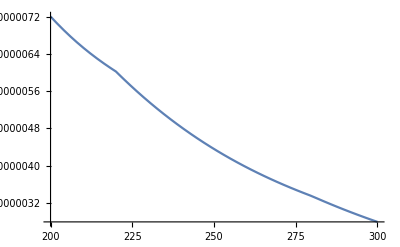

```mathematica
Plot[f1[Mass],{Mass,200,300}]
```

```mathematica
f1[300]
```

2.79436×10^-6

```mathematica
F1=Integrate[f1[x],x]
```

InterpolatingFunction[…][x]

InterpolatingFunction::dmval: Input value {50.0031} lies outside the range of data in the interpolating function. Extrapolation will be used.

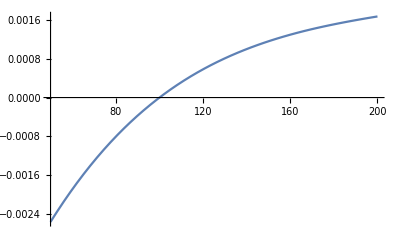

```mathematica
Plot[F1,{x,50,200}]
```

```mathematica
F1[100]
```

InterpolatingFunction[…][x][100]

```mathematica
FindMaximum[F1,x]
```

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.00253245,{x→880.168}}

```mathematica
ResourceFunction["Intercepts"][y==3 x+5,{x,y}]
```

<|x→{{-5/3,0}},y→{{0,5}}|>

```mathematica
ResourceFunction["Intercepts"][F1[Mass]]
```

[InterpolatingFunction[…][x][{100.,160.,220.,280.,340.,400.,460.,520.,580.,640.,700.}]]